# Partial mimicry project

## Import Network

```mathematica
net = Import["/Users/dinesh/Dropbox/projects/partial mimicry/PartialMimicryTrainingPhotos/TrainedSpiderClassifier3.m"]
```

NetChain[<>]

## Tests

### 0. Does the net work?

```mathematica
jspider = -Graphics-; antmimic=-Graphics-;antmimicface= -Graphics-;
```

```mathematica
net[{jspider,antmimic,antmimicface},"Probabilities"]
```

{<|Spider→0.99904,NonSpider→0.000960185|>,<|Spider→0.62725,NonSpider→0.37275|>,<|Spider→0.8762,NonSpider→0.1238|>}

```mathematica
BarChart[net[{jspider,antmimic,antmimicface},"Probabilities"][[All,1]],ChartLabels->{-Graphics-,-Graphics-,-Graphics-}, FrameLabel->True,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Jumping spiders"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["/Users/dinesh/Desktop/Untitled.pdf",%7,"PDF"]
```

/Users/dinesh/Desktop/Untitled.pdf

### 1. Proof of concept with Rhagoletis pomonella and Ceratitis capitata

```mathematica
rp= -Graphics-;cc=-Graphics-;hf=-Graphics-;
```

```mathematica
net[{rp,cc,hf},"Probabilities"]
```

{<|Spider→0.403639,NonSpider→0.596361|>,<|Spider→0.716104,NonSpider→0.283896|>,<|Spider→0.00938015,NonSpider→0.99062|>}

```mathematica
{<|"Spider"->0.40363869071006775,"NonSpider"->0.5963612794876099|>,<|"Spider"->0.7161040902137756,"NonSpider"->0.283895879983902|>}
```

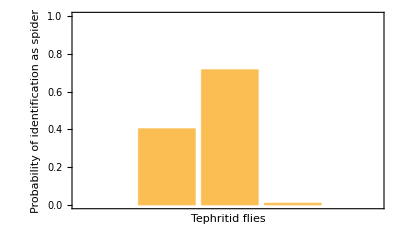

```mathematica
BarChart[net[{rp,cc,hf},"Probabilities"][[All,1]],ChartLabels->{-Graphics-,-Graphics-,-Graphics-},Frame->True,FrameStyle->Black,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Tephritid flies"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}, PlotRange->{0,1}]
```

### 2. Other salticid mimicking insects

```mathematica
insects = {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
mView=net[#,"Probabilities"]&/@insects
```

{<|Spider→0.937588,NonSpider→0.0624123|>,<|Spider→0.903327,NonSpider→0.0966734|>,<|Spider→0.621224,NonSpider→0.378776|>,<|Spider→0.604773,NonSpider→0.395227|>,<|Spider→0.514051,NonSpider→0.485949|>,<|Spider→0.000851838,NonSpider→0.999148|>}

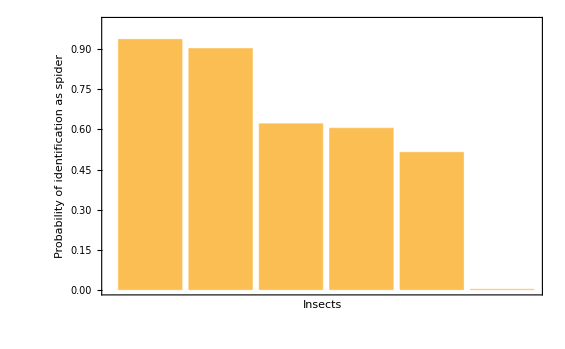

```mathematica
BarChart[mView[[All,1]],ChartLabels->insects, Frame->True,FrameStyle->Black,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Insects"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},PlotRange->{0,1}]
```

### 3. An example fly species from different angles

```mathematica
ceratitis= {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
cpView=net[#,"Probabilities"]&/@ceratitis
```

{<|Spider→0.956435,NonSpider→0.0435652|>,<|Spider→0.283671,NonSpider→0.716329|>,<|Spider→0.159346,NonSpider→0.840654|>,<|Spider→0.144426,NonSpider→0.855574|>,<|Spider→0.108901,NonSpider→0.891099|>,<|Spider→0.106867,NonSpider→0.893133|>,<|Spider→0.082129,NonSpider→0.917871|>}

```mathematica
ceratitisimgs=ImageResize[#, 275]&/@ceratitis
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

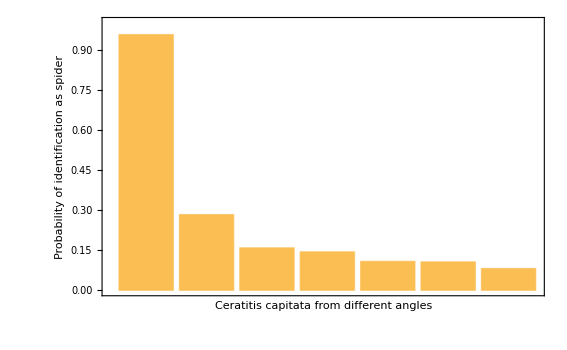

```mathematica
BarChart[cpView[[All,1]],ChartLabels->ceratitisimgs, Frame->True,FrameStyle->Black,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Ceratitis capitata from different angles"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},PlotRange->{0,1}]
```

#### 4A. Incorporating visual acuity (uncorrected,5, 8, 10 cm distance) Wasp visual system with cpd of 1.2

```mathematica
visac={-Graphics-,-Graphics- ,-Graphics-,-Graphics-};
```

```mathematica
visac2=ImageResize[#, 275]&/@visac
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
vaView=net[visac2,"Probabilities"]
```

{<|Spider→0.956435,NonSpider→0.0435652|>,<|Spider→0.944169,NonSpider→0.055831|>,<|Spider→0.860901,NonSpider→0.139099|>,<|Spider→0.717645,NonSpider→0.282355|>}

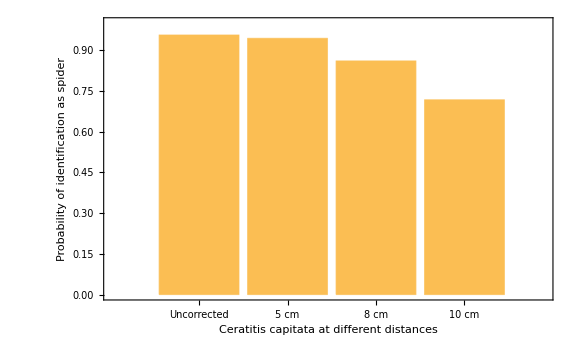

```mathematica
BarChart[vaView[[All,1]], Frame->True,FrameStyle->Black,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Ceratitis capitata at different distances"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},FrameTicks->{{Automatic,Automatic},{{{1,"Uncorrected"},{2,"5 cm"},{3,"8 cm"},{4,"10 cm"}},Automatic}},PlotRange->{0,1}, ChartLabels->visac2]
```

### 4B. Incorporating visual acuity (uncorrected,5, 8, 10 cm distance) jumping spider visual system with cpd of 3.86 (phidippus)

```mathematica
visacphid={-Graphics-,-Graphics-,-Graphics-,-Graphics- }
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visacphid2=ImageResize[#, 275]&/@visacphid
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
spView=net[visacphid2,"Probabilities"]
```

{<|Spider→0.956435,NonSpider→0.0435652|>,<|Spider→0.957306,NonSpider→0.0426937|>,<|Spider→0.951927,NonSpider→0.0480731|>,<|Spider→0.984957,NonSpider→0.0150435|>}

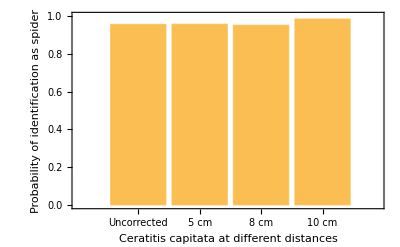

```mathematica
BarChart[spView[[All,1]], Frame->True,FrameStyle->Black,FrameLabel->{{HoldForm[Probability of identification as spider],None},{HoldForm["Ceratitis capitata at different distances"],None}},PlotLabel->None,LabelStyle->{16,GrayLevel[0]},FrameTicks->{{Automatic,Automatic},{{{1,"Uncorrected"},{2,"5 cm"},{3,"8 cm"},{4,"10 cm"}},Automatic}},PlotRange->{0,1}, ChartLabels->visacphid2]
```

## Discussion

#### Deepdream image: What does the net use to detect spiders?

```mathematica
spider=-Graphics-
```

-Graphics-

```mathematica
nonspider=-Graphics-
```

-Graphics-

```mathematica
deepdream = { spider,nonspider}
```

{-Graphics-,-Graphics-}

```mathematica
netView=net[deepdream,"Probabilities"]//N
```

{<|Spider→1.,NonSpider→9.10528×10^-11|>,<|Spider→2.74632×10^-9NonSpider→1.|>}

```mathematica
netview2={{1,0},{0,1}}
```

{{1,0},{0,1}}

### Photolinks

test0 
https://www.flickr.com/photos/nickadel/34870124860/
https://www.flickr.com/photos/nickadel/37205626390/

## Other insects

image1 https://twitter.com/singaporemacro/status/1358611723133935616?s=20&t=fz0NguYLfrG2Ug6IkVDelA
image2 https://commons.wikimedia.org/wiki/File:Olethreutes_arcuella_side.jpg
image3  https://twitter.com/elaphrornis/status/1603530324918652932?s=20&t=fz0NguYLfrG2Ug6IkVDelA
image4 https://www.flickr.com/photos/pasha_k/16891823956
image5 https://inaturalist.ca/observations/14685506
image 6 https://www.brisbaneinsects.com/brisbane_planthoppers/AcaciaHopper1.htm